## Setup of Environment

```mathematica
$Assumptions={Element[a0,Integers], Element[a1,Integers],Element[a2,Integers]};
```

```mathematica
Clear[a0,a1,a2,b0,b1,b2];
Format[a0]:=Subscript[a, 0]
Format[a1]:=Subscript[a, 1]
Format[a2]:=Subscript[a, 2]
Format[b0]:=Subscript[b, 0]
Format[b1]:=Subscript[b, 1]
Format[b2]:=Subscript[b, 2]
```

Number of Input Bits: a1,a0,b1,b0

```mathematica
n=4;
```

### Rules

Definition of calculating in binary using rules, e.g. a0 + a0 = 2·a0 = 0, a0·a0 = a0^2 = a0

```mathematica
Mod2Rules={
x_Integer /;EvenQ[x]->0,
x_Integer/;OddQ[x]->1
};
PowRules={Power[x_,_]->x};
BinRules=Union[Mod2Rules,PowRules];
```

Mask the multiplications a0·a1 and a0 a1 with the single symbol a0a1 in order to avoid that FreeQ detects a0 or a1 in the multiplications. Same with b0·b1.

```mathematica
MaskMultRule={a0 a1->a0a1,b0 b1->b0b1};
```

### Dictionaries / Associations

```mathematica
IdentityRules={a0->a0,a1->a1};
```

Affine transformations for the first canonization step. Maps the term to the transformation: When the term is found in the first summand of the IC statement, the corresponding transformation should be applied.

```mathematica
CanonTransformationRules1 = <|
0->IdentityRules,
a0->IdentityRules,
a1->{a0->a1,a1->a0},
a0+a1->{a0->a0+a1,a1->a1},
a0 a1->IdentityRules,
a0+a0 a1->{a0->a0,a1->a1+1},
a1+a0 a1->{a0->a0+1,a1->a1},
a0+a1+a0 a1->{a0->a0+a1,a1->a1+1} 
|>;
```

Affine transformations for the second canonization step. Maps two terms to the transformation: If the first term is found in the first summand of the IC statement and the second term is found in the second term of the IC statement, the corresponding transformation should be applied.

```mathematica
CanonTransformationRules2 = <|
{0,0}->IdentityRules,
{a0,0}->IdentityRules,
{a0,a1}->IdentityRules,
{a0,a0 a1}->IdentityRules,
{a0,a0 a1+a1}->{a0->a0+1,a1->a1},
{a0 a1,0}->IdentityRules,
{a0 a1,a0}->IdentityRules,
{a0 a1,a1}->{a0->a1,a1->a0},
{a0 a1,a0+a1}->{a0->a0+a1+1,a1->a1}
|>;
```

Association which maps the canonized IC statement to its name as given in the paper.

```mathematica
ClassNames:=<|
{0,0,0,0}->"Class 1",
{II["g",a0,"b",{}],0,0,0}->"Class 2",
{II["g",a0 a1,"b",{}],0,0,0}->"Class 3",
{II["g",a0,"b",{}],II["g",a1,"b",{a0}],0,0}->"Class 4",
{II["g",a0,"b",{}],II["g",a0 a1,"b",{a0}],0,0}->"Class 5",
{II["g",a0 a1,"b",{}],II["g",a0,"b",{a0 a1}],0,0}->"Class 6",
{II["g",a0,"b",{}],II["g",a0 a1,"b",{a0}],II["g",a1,"b",{a0,a0 a1}],0}->"Class 7",
{II["g",a0 a1,"b",{}],II["g",a0,"b",{a0 a1}],II["g",a1,"b",{a0,a0 a1}],0}->"Class 8"
|>
```

### Helper Functions

If the given expression is part of the term, the expression will be removed from the term by subtracting it. Otherwise the term will be returned unchanged.

```mathematica
RemoveExprFromTerm[term_, expr_]:=If[FreeQ[term/.MaskMultRule, expr/.MaskMultRule], term, term-expr];
```

Removes the given expression from every term in the given set. For example removes the constant 1 from every term: {a0 + 1, a0 a1+1} to {a0, a0 a1}.
First apply the reduction to every item in the set, then delete possible duplicate elements and the element 0.

```mathematica
RemoveExprFromTermSet[set_,expr_]:=DeleteElements[DeleteDuplicates[(RemoveExprFromTerm[#,expr])&/@ set],{0}]
```

Simplifies a binary expression, e.g. 2 a0 + 3 a1 + a2 * a2 = a1 + a2

```mathematica
SimplifyBinary[expr_]:=PolynomialMod[ExpandAll[expr,Modulus->2]/.PowRules,2];
```

Sort the given statements by the b value.

```mathematica
SortByBValue[stmt_]:=SortBy[stmt,(Level[#,1][[3]])&];
```

Sorts the given statement by the length of the conditional set X_b.

```mathematica
SortBySetLength[stmt_]:=SortBy[stmt,(Length[Level[#,1][[4]]])&]
```

Sorts the given MI statements. Splits the given statements into the non-zero ones and into the ones which equal zero (II[_, 0, _, _]). Sorts the non-zero ones by the length of the conditional set and the zero ones by the b value and concatenates the resulting list.

```mathematica
SortStatement[stmt_]:=Flatten[{SortBySetLength[DeleteCases[stmt,II[_,0,_,_]]],SortByBValue[Cases[stmt,II[_,0,_,_]]]}]
```

Get the Class name from a MIS statement in canonized form.

```mathematica
GetClass[v_]:=Module[{TermAndConditionalSet,StatementWithoutBValue},
(* Extract Term and Conditional Set from all elements except when they are zero *)
TermAndConditionalSet=(If[#===0,0,Level[#,1][[{2,4}]]])&/@v;

(* Construct II again from Term and Cond Set but without b value this time*)
StatementWithoutBValue=(If[#===0,0,II["g",#[[1]],"b",#[[2]]]])&/@TermAndConditionalSet;

(* Lookup Statement in association *)
ClassNames[StatementWithoutBValue]
]
```

#### Useful Sets

All Expressions which don’t contain a b value.

```mathematica
AllAExpressions=Total/@Subsets[{1,a0,a1,a0 a1}]
```

{0,1,a_0,a_1,a_0 a_1,1+a_0,1+a_1,1+a_0 a_1,a_0+a_1,a_0+a_0 a_1,a_1+a_0 a_1,1+a_0+a_1,1+a_0+a_0 a_1,1+a_1+a_0 a_1,a_0+a_1+a_0 a_1,1+a_0+a_1+a_0 a_1}

All Expressions containing a0·a1

```mathematica
AllA0A1Expressions=Select[AllAExpressions,(Not[FreeQ[#,a0 a1]])&]
```

{a_0 a_1,1+a_0 a_1,a_0+a_0 a_1,a_1+a_0 a_1,1+a_0+a_0 a_1,1+a_1+a_0 a_1,a_0+a_1+a_0 a_1,1+a_0+a_1+a_0 a_1}

## Creation of Conditional Set (Minimal Generating Set)

### Alternative 1

Iterates over the given set, looks at the current element and tries to reduce this element from every following element in the set.
E.g. {a0, a0+a0 a1,a1+a0 a1} → {a0,a0 a1,a1}

```mathematica
ReduceIterateSet[set_]:=Module[{Result,ReductionElement,FollowingElement,i,j},
Result=set;

(*Iterate over every element in the set*)
For[i = 1,i<Length[set],i++,
ReductionElement=Result[[i]];

(*Look at every following elements in the set.*)
For[j=i+1,j<=Length[set],j++,
(*Remove the reduction element from the current element and store it at the same index in the set*)
FollowingElement=Result[[j]];
Result[[j]]=RemoveExprFromTerm[FollowingElement, ReductionElement];
];
];

(*Reduction might yield 0, remove these elements*)
Result=DeleteElements[Result,{0}];

Result
];
```

Tries to figure out if elements from the set can be constructed by adding two other elements from the set.
Iterates over the given set, adds the current element and every following element. The result will be removed from the set.
E.g.: {a0+a1,a0+a0 a1,a1+a0 a1}->{a0+a1,a0+a0 a1}

```mathematica
AddIterateSet[set_]:=Module[{Result,ElementsToDelete,AddedTerm,i,j},
(*Sort the elements in ascending order*)
Result=Sort[set];

For[i = 1, i <= Length[Result], i++,
For[j = i + 1, j <= Length[Result], j++,
(*Add the current element and all following element*)
AddedTerm=SimplifyBinary[Result[[i]]+Result[[j]]];

(*Remove the result from the set, if it already exists in the set*)
Result=DeleteElements[Result,{AddedTerm}];
];
];

Result
]
```

Uses the conditioning  set X_b to create a set which only contains the necessary building blocks, from which every element in X_b can be constructed (Minimal Generating Set).
E . g . {a0, a0 + a0 a1, a1 + a0 a1} -> {a0, a1}

```mathematica
ConditionalSetAlt1[set_]:=Module[{Result, CurrentSet, SetsDifferentQ},

(*Remove the constant 1 from every element in the set*)
CurrentSet=RemoveExprFromTermSet[set,1];
(*Sort the input set*)
CurrentSet=Sort[CurrentSet];

(*Indicates if the previous set and the processed set are different*)
SetsDifferentQ=True;

(*Iterate as long as the previous set and the processed set are different*)
While[SetsDifferentQ,
(*Construct the new set from the current set*)
Result=Sort[ReduceIterateSet[CurrentSet]];
Result=Sort[AddIterateSet[Result]];

(*If the set contains a0 and a1 we can construct all expression from these. Break and return {a0, a1}*)
If[ContainsAll[Result,{a0,a1}],Return[{a0,a1}]];

If[CurrentSet===Result,
(*Sets are the same, break from loop*)
 SetsDifferentQ=False,
(*Sets are different. Use the new set as the input for the next iteration.*)
 CurrentSet = Result
];
];

Result
];
```

### Alternative 2

Uses the conditioning  set X_b to create a set which only contains the necessary building blocks, from which every element in X_b can be constructed (Minimal Generating Set) .
E . g . {a0, a0 + a0 a1, a1 + a0 a1} -> {a0, a1}

```mathematica
ConditionalSetAlt2[set_]:=Module[{Result},

(*Remove the constant 1 from every element in the set*)
Result=RemoveExprFromTermSet[set,1];
(*Sort the input set*)
Result=Sort[Result];

(*Apply methods until set does not change anymore*)
Result=FixedPoint[(Sort[AddIterateSet[Sort[ReduceIterateSet[#]]]])&,Result];

If[ContainsAll[Result,{a0,a1}],{a0,a1},Result]
];
```

### Alternative 3

```mathematica
SplitAddition[set_]:=Flatten[{set /.Plus[fst:_,rst:__]->List[fst,rst]}];(* Maybe replace repeated? //. *)
```

```mathematica
MapToVector[term_,basis_]:=(If[MemberQ[SplitAddition[term],#],1,0])&/@basis;
```

```mathematica
DeleteMultRedundancy[expr_,set_]:=Module[{setWithoutExpr,ProdSet},
setWithoutExpr=DeleteElements[set,{expr}];
ProdSet=Fold[(Flatten[TensorProduct[#1,Flatten[{1,#2}]]])&,{1},setWithoutExpr];

If[MemberQ[ProdSet,expr],0,expr]
]
```

```mathematica
ConditionalSetAlt3[{___Integer}]={};
```

```mathematica
ConditionalSetAlt3[set_]:=Module[{setWithoutConst,basis,matrix,reduced},
setWithoutConst=RemoveExprFromTermSet[set,1];

basis=DeleteDuplicates[SplitAddition[setWithoutConst]];
basis=Reverse[Sort[basis]];

matrix=MapToVector[#,basis]&/@setWithoutConst;

reduced=DeleteElements[RowReduce[matrix,Modulus->2].basis,{0}];

Sort[DeleteElements[(If[Head[#]===Times,DeleteMultRedundancy[#,reduced],#])&/@reduced,{0}]]
]
```

### Function Call

```mathematica
ConditionalSet[set_]:=ConditionalSetAlt2[set];
```

## Reduction Function

Reduces the expression with the values from the given set. Returns the expression and a minimal generating set with the basic building blocks, being able to construct the original set.

```mathematica
Reduction[term_, set_]:=
Module[{TermWithoutConstant,CondSet,AddSet,ProductSet,ConditionalSetWithOne,ReducedTerm},
(* Remove the constant 1 from the term if it exists, e.g. a0 + 1 to a0 *)
TermWithoutConstant=RemoveExprFromTerm[term,1];

(*Construct the conditional set, which contains only the basic building blocks*)
CondSet = ConditionalSet[set];
 
(*Add all elements from the minimal generating set together in order to be able to construct all possible elements, which can be derived from these elements. 
Add 0 in order to preserve the singleton elements*)
AddSet=(Plus @@@Subsets[Union[CondSet,{0}],{2}])//.Mod2Rules//DeleteElements[#,{0}]&//DeleteDuplicates;

(*Add one to the conditional set. When creating the product set, we want to preserve the singleton elements from this set, therefore we add one to this set.
Because when multiplying with one, the elements stay in the set.*)
ConditionalSetWithOne = Union[AddSet,{1}];
(*Create the product set by creating all possible subsets of length 2 and then multiplying the elements in these sets*)
ProductSet=(Times @@@Subsets[ConditionalSetWithOne,{2}])//DeleteDuplicates;

(*Reduce the given term by trying to remove every element in the product set from the term*)
ReducedTerm=Fold[RemoveExprFromTerm,TermWithoutConstant,ProductSet];

{ReducedTerm,CondSet}
]
```

## 4-bit Binary Functions Definition

Some important functions.

```mathematica
IP[a1_, a0_, b1_, b0_] :=a0 b0+a1 b1
DISJ[a1_, a0_, b1_, b0_] := 1 +a0 b0 + a1 b1 + a0 b0 a1 b1
EQ[a1_, a0_, b1_, b0_]:=a0 a1+ a0 b1+a0+b0 a1+b0 b1+b0+a1+b1+1
INDEX[a1_,a0_,b1_,b0_]:=a0+a0 b0+a1 b0 (*(b0+1)·a0 + a1·b0*)
```

Definition of all binary functions with four bits as input. BitGet[n,x] gets the constant c^x term for the function. Each function has 16 constants (c^0 - c^15). Enumerating n from 0 to 2^2^n-1 produces all 65536 functions.

```mathematica
f00[num_,b1_,b0_]:=(b1+1)(b0+1)BitGet[num,0]+(b1+1) b0 BitGet[num,1]+b1(b0+1) BitGet[num,2] + b0 b1 BitGet[num,3]
f01[num_,b1_,b0_]:=(b1+1)(b0+1)BitGet[num,4]+(b1+1) b0 BitGet[num,5]+b1(b0+1) BitGet[num,6] + b0 b1 BitGet[num,7]
f10[num_,b1_,b0_]:=(b1+1)(b0+1)BitGet[num,8]+(b1+1) b0 BitGet[num,9]+b1(b0+1) BitGet[num,10] + b0 b1 BitGet[num,11]
f11[num_,b1_,b0_]:=(b1+1)(b0+1)BitGet[num,12]+(b1+1) b0 BitGet[num,13]+b1(b0+1) BitGet[num,14] + b0 b1 BitGet[num,15]
```

Function in factorized form .

```mathematica
FFac[num_] :=Function[{a1,a0,b1,b0},
(a1+1)(a0+1)f00[num,b1,b0]+
(a1+1)(a0) f01[num,b1,b0]+
(a1)(a0+1)f10[num,b1,b0]+
(a1)( a0) f11[num,b1,b0]
]
```

Function in expanded form .

```mathematica
F[num_] :=Function[{a1,a0,b1,b0},
SimplifyBinary[
FFac[num][a1,a0,b1,b0]
]
]
```

Returns the function expression for the given function number.

```mathematica
FExpr[num_]:=F[num][a1,a0,b1,b0]
```

Complement function: f[x]=1 - f_complement[x]

```mathematica
FComplement[num_]:=F[2^2^n-1-num]
```

Prints out all possible combination of 4 bit inputs and the corresponding function output.

```mathematica
FunctionTruthTable[num_]:=Flatten[Table[{a1,a0,b1,b0}->F[num][a1,a0,b1,b0],{a1,0,1},{a0,0,1},{b1,0,1},{b0,0,1}]];
```

Gives back the function number for a given expression

```mathematica
FNumberFromExpression[expr_]:=Module[{Binary},
Binary=Flatten[Table[SimplifyBinary[expr/.{a1->a1Val,a0->a0Val,b1->b1Val,b0->b0Val}],{a1Val,0,1},{a0Val,0,1},{b1Val,0,1},{b0Val,0,1}]];
FromDigits[Reverse[Binary],2]
]
```

Takes four expressions, which are the result of the assignment of the b values (00,01,10,11). Returns the function expression, which matches the input.

```mathematica
FExprFromBParts[f00_,f01_,f10_,f11_]:=SimplifyBinary[(b1+1)(b0+1)f00+(b1+1)b0 f01+b1(b0 +1)f10+b1 b0 f11]
```

Calculates the expressions of f(a_1,a_0,0,0),f(a_1,a_0,0,1),f(a_1,a_0,1,0),f(a_1,a_0,1,1) for a given function number.

```mathematica
FNumToParts[num_]:={F[num][a1,a0,0,0],F[num][a1,a0,0,1],F[num][a1,a0,1,0],F[num][a1,a0,1,1]}
```

## Affine Transformations

All invertible Matrices.

```mathematica
MatrizesI={{{1,0},{0,1}},{{0,1},{1,0}},{{0,1},{1,1}},{{1,0},{1,1}},{{1,1},{1,0}},{{1,1},{0,1}}};
```

Vector with a0 and a1 .

```mathematica
avec={a0, a1};
```

Get all affine transformations by multiplying the invertible matrices with the vector and adding constants 0 and 1.

```mathematica
AffineTransformationRule[i_, j_, k_]:={a0->(MatrizesI[[k]].avec)[[1]]+i, a1->(MatrizesI[[k]].avec)[[2]]+j}
```

```mathematica
AffineTransformationRules=Flatten[Table[AffineTransformationRule[i,j,k],{i,0,1},{j,0,1},{k,1,6}],2]
```

{{a_0→a_0,a_1→a_1},{a_0→a_1,a_1→a_0},{a_0→a_1,a_1→a_0+a_1},{a_0→a_0,a_1→a_0+a_1},{a_0→a_0+a_1,a_1→a_0},{a_0→a_0+a_1,a_1→a_1},{a_0→a_0,a_1→1+a_1},{a_0→a_1,a_1→1+a_0},{a_0→a_1,a_1→1+a_0+a_1},{a_0→a_0,a_1→1+a_0+a_1},{a_0→a_0+a_1,a_1→1+a_0},{a_0→a_0+a_1,a_1→1+a_1},{a_0→1+a_0,a_1→a_1},{a_0→1+a_1,a_1→a_0},{a_0→1+a_1,a_1→a_0+a_1},{a_0→1+a_0,a_1→a_0+a_1},{a_0→1+a_0+a_1,a_1→a_0},{a_0→1+a_0+a_1,a_1→a_1},{a_0→1+a_0,a_1→1+a_1},{a_0→1+a_1,a_1→1+a_0},{a_0→1+a_1,a_1→1+a_0+a_1},{a_0→1+a_0,a_1→1+a_0+a_1},{a_0→1+a_0+a_1,a_1→1+a_0},{a_0→1+a_0+a_1,a_1→1+a_1}}

```mathematica
Length[AffineTransformationRules]
```

24

Applies all affine transformations to a given expr.

```mathematica
ApplyAllAffineTransformations[expr_]:=SimplifyBinary/@((expr/.#)&/@AffineTransformationRules);
```

## Non-Local AND Operations

Counts the number of non-local AND operations for the given expression.

```mathematica
CountNLAndInExpr[expr_]:=Module[{Expr,Coefficients,n1,n2,Coefficients1,Coefficients2,ContainesA0A1},
Expr=Expand[expr];

(* Check if the expression contains a "a0·a1" *)
ContainesA0A1=Not[FreeQ[Expr,a0 a1]];

If[ContainesA0A1,
(* Expression contains "a0·a1" *)

(* Mask "a0·a1" in order to be able to set it to zero and get its coefficients*)
Expr=Expr/.a0 a1->a0a1;

(* a0, a1 coefficients*)
(* Get coefficient rules for a0, a1 without "a0·a1" by setting it to zero *)
Coefficients1=CoefficientRules[Expr/.a0a1->0,{a0,a1}];
(* drop the coefficients which do not depend on a0, a1 ({0,0}), e.g. in the expression b0 + b1. They do not contribute to a non-local and. *)
Coefficients1=KeyDrop[Coefficients1,{{0,0}}];
Coefficients1=Values[Coefficients1];
(* Set all integer values in the coefficients to zero, because these represent a0, a1 constants. They also do not contribute to a non-local and. *)
Coefficients1=DeleteElements[Coefficients1/.{_Integer->0},{0}];
(* Delete duplicates because if a0 and a1 have the same coefficients this results in only one non-local and *)
Coefficients1=DeleteDuplicates[Coefficients1];

(* "a0·a1" coefficients *)
(* Get the coefficient for "a0·a1" *)
Coefficients2=Coefficient[Expr,a0a1];
(* Set all integer values in the coefficients to zero, because these represent "a0·a1" as a constant. They do not contribute to a non-local and. *)
Coefficients2=DeleteElements[{Coefficients2/.{_Integer->0}},{0}];

(* Get linearly independent elements from bots coefficient sets *)
Coefficients=ConditionalSet[Union[Coefficients1,Coefficients2]];

(* Count the number of final coefficients *)
Length[Coefficients]
,

(* Expression does not contain "a0·a1" *)
(* Get the coefficient rules for a0, a1 *)
Coefficients=CoefficientRules[Expr,{a0,a1}];
(* drop the coefficients which do not depend on a0, a1 ({0,0}), e.g. in the expression b0 + b1. They do not contribute to a non-local and. *)
Coefficients=KeyDrop[Coefficients,{{0,0}}];
Coefficients=Values[Coefficients];
(* Set all integer values in the coefficients to zero, because these represent a0, a1 constants. They also do not contribute to a non-local and. *)
Coefficients=DeleteElements[Coefficients/.{_Integer->0},{0}];
(* Delete duplicates because if a0 and a1 have the same coefficients this results in only one non-local and *)
Coefficients=DeleteDuplicates[Coefficients];

(* Count the number of final coefficients *)
Length[Coefficients]
]
]
```

Counts the number of non - local AND operations for the given expression .

```mathematica
CountNLAndInExpr2[expr_]:=Module[{Expr,Coefficients,Coefficients1,Coefficients2,Coefficients3},
Expr=Expand[expr];

Expr=Expr/.{a0 a1->a0a1};

Coefficients1=Coefficient[Expr,a1];
Coefficients2=Coefficient[Expr,a0];
Coefficients3=Coefficient[Expr,a0a1];

Coefficients={Coefficients1,Coefficients2,Coefficients3};
(* Set all integer values in the coefficients to zero, because these represent a0, a1 constants. They also do not contribute to a non-local and. *)
Coefficients=DeleteElements[Coefficients/.{_Integer->0},{0}];
(* Delete duplicates because if a0 and a1 have the same coefficients this results in only one non-local and *)
Coefficients=DeleteDuplicates[Coefficients];

(* Count the number of final coefficients *)
Length[ConditionalSet[Coefficients]]
]
```

Returns the number of non - local ands for the given function .

```mathematica
CountNLAnd[fun_]:=CountNLAndInExpr[fun[a1,a0,b1,b0]];
```

## Mutual Information Sum Definition

Definition of set X_b. fun is the function which should be called with concrete b1 and b0 values. idxs gives the ordering of the b values, e.g. for the ordering {1,3,0,2} the function Xb will be called with the idxs {}, {1}, {1,3} and {1,3,0}.

```mathematica
Xb[fun_, idxs_] :=SimplifyBinary/@(fun[a1, a0, BitGet[#, 1], BitGet[#, 0]])&/@idxs;
```

Definition of the Mutual Information Sum. fun is the function and ord describes the ordering. Returns a list of summands and not summation (Mathemtica sometimes orders the summands in a sum weird and in this way we preserve the ordering of ord).

```mathematica
MIS[fun_,ord_:{0,1,2,3}]:=(II["g",SimplifyBinary[fun[a1,a0,BitGet[ord[[#]], 1],BitGet[ord[[#]],0]]],ord[[#]], Xb[fun, ord[[1;;#-1]]]])&/@Range[1,n];
```

Reduces a Mutual Information statement. Break it up, reduce the term, construct a new statement from the reduced term and the conditional set

```mathematica
ReduceMI[ii_]:=Level[ii, 1]//(Reduction[#[[2]], #[[4]]])&//(II["g", #[[1]], Level[ii,1][[3]],#[[2]]])&
```

Reduced mutual information sum. Construct the normal MIS and then reduces each statement individually

```mathematica
MISReduced[fun_,ord_:{0,1,2,3}]:=  ReduceMI /@ MIS[fun,ord]
```

## Canonical Form

Gets the term from a mutual information statement.

```mathematica
GetTermValue[ii_]:=Level[ii,1][[2]];
```

Gets the term value from the first mutual information statement.

```mathematica
GetFirstTermValue[stmt_]:=GetTermValue[stmt[[1]]];
```

Gets the term value from the second mutual information statement .

```mathematica
GetSecondTermValue[stmt_]:=GetTermValue[stmt[[2]]];
```

Return the affine Transformation based on the term of the first mutual information statement .

```mathematica
GetCanonTransformationRule1[stmt_]:=CanonTransformationRules1[GetFirstTermValue[stmt]];
```

Return the affine Transformation based on the term of first and the second mutual information statement .

```mathematica
GetCanonTransformationRule2[stmt_,fstterm_]:=CanonTransformationRules2[{fstterm,GetSecondTermValue[stmt]}];
```

Applies the binary rules to the term and the conditional set of the given mutual information statement .

```mathematica
ApplyBinaryRules[term_]:=Level[term,1]//II["g",SimplifyBinary[#[[2]]],#[[3]],SimplifyBinary[#[[4]]]]&
```

Transforms the given IC statement based on the supplied affine transformation . This function also reduces the result of the transformation .

```mathematica
TransformStatement[stm_, rule_]:=Module[{TransformedStmt},
(* Apply the rule (affine transformation) to the whole ic statement. *)
TransformedStmt = stm/.rule;

(* Make sure the result of the transformation is valid in binary. *)
TransformedStmt = ApplyBinaryRules/@(TransformedStmt//ExpandAll);

(* Apply the usual reduction to the result of the transformation. *)
TransformedStmt= ReduceMI/@TransformedStmt;

TransformedStmt
];
```

Returns the IC statement of the given function in a canonized form .

```mathematica
CanonizedMIS[fun_,ord_:{0,1,2,3}]:=Module[{Stmt,SortedStmt,FirstRule,FirstTransformation,SecondRule,SecondTransformation,RemoveBVal},
(* Calculate the reduced IC statement of the function. *)
Stmt=MISReduced[fun,ord];
(* Sort parts of the IC statement, e.g. zeros to the back. *)
SortedStmt=SortStatement[Stmt];

(* Get the first transformation rule based on the current statement and apply it to the statement. *)
FirstRule=GetCanonTransformationRule1[SortedStmt];
FirstTransformation=SortStatement[TransformStatement[SortedStmt,FirstRule]];

(* Get the second transformation rule based on the first transformation and apply it to the transformed statement. *)
SecondRule=GetCanonTransformationRule2[FirstTransformation,GetFirstTermValue[FirstTransformation]];
SecondTransformation=SortStatement[TransformStatement[FirstTransformation,SecondRule]];

(*RemoveBVal=SecondTransformation/.II[g_,t_,b_,xb_]->II[g,t,"b",xb];*)

(* Map mutual information with zero terms to zero. *)
SecondTransformation/.II[g_,0,b_,xb_]->0
]
```

Calculate the canonized IC statements for a function for all possible orderings .

```mathematica
CanonizedMISAllOrderings[fun_]:=Table[ord->{CanonizedMIS[fun,ord],GetClass[CanonizedMIS[fun,ord]]},{ord,Permutations[{1,2,3,4}]}]
```

## Canonize All Functions

```mathematica
DistributeDefinitions[IdentityRules];
DistributeDefinitions[CanonTransformationRules1];
DistributeDefinitions[CanonTransformationRules2];
```

Set working directory to directory of the notebook.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Simon\Desktop\Thesis_InformationCausality

Compute the canonical form for every function. Outputs a list of tuples containing function number and canonical form of that function.

```mathematica
fNameAndCanonForm=ParallelTable[{j,CanonizedMIS[F[j],{0,1,2,3}]},{j,0,2^2^n-1}]
```

```mathematica
Export["fNameAndCanonForm.wdx",fNameAndCanonForm];
```

Compute the canonical form for every function in every possible ordering.

```mathematica
fNameAndCanonFormAllOrderings=Association[Table[ord->ParallelTable[{j,CanonizedMIS[F[j],ord],ord},{j,0,2^2^n-1}],{ord,Permutations[{0,1,2,3}]}]]
```

```mathematica
Timing[Association[Table[ord->ParallelTable[{j,CanonizedMIS[F[j],ord],ord},{j,0,2^2^n-1}],{ord,Permutations[{0,1,2,3}]}]]]
```

```mathematica
Export["fNameAndCanonFormAllOrderings.wdx",fNameAndCanonFormAllOrderings];
```

Import the previously calculated classifications.

```mathematica
fNameAndCanonFormAllOrderings=Import["fNameAndCanonFormAllOrderings.wdx"];
```

```mathematica
fNameAndCanonForm=Import["fNameAndCanonForm.wdx"];
```

Reset the directory to the normal working directory.

```mathematica
ResetDirectory[];
```

## Classify Functions

Maps class name to a list of function numbers, which are in that class.

```mathematica
groupedByClass=GroupBy[fNameAndCanonForm,(GetClass[#[[2]]])&->First]
```

For all 24 different orderings: Maps class name to a list of function numbers, which are in that class.

```mathematica
groupedByClassAllOrderings=Map[(GroupBy[#,(GetClass[#[[2]]])&->First])&,fNameAndCanonFormAllOrderings]
```

Map each function to a list of class-ordering tuples it belongs to.

```mathematica
classAndOrderingByFunctionName=GroupBy[Flatten[Values[fNameAndCanonFormAllOrderings],1],(First)->(({GetClass[#[[2]]],#[[3]]})&)]
```

Map each function to a list of classes it belongs to.

```mathematica
classCombByFunctionName=DeleteDuplicates/@Association[KeyValueMap[(#1->#2[[All,1]])&,classAndOrderingByFunctionName]]
```

Map each possible class combination to a list of functions . These functions are in one of the classes for a certain ordering .

```mathematica
fNameByClassComb=GroupBy[KeyValueMap[((Sort[#2])->(#1))&,classCombByFunctionName],(First)->((#[[2]])&)]
```

Counts how many functions are in each class .

```mathematica
sizesClasses=Sort[KeyValueMap[({#1,Length[#2]})&,groupedByClass]]
```

{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}}

For all 24 different orderings : Counts how many functions are in each class.

```mathematica
sizesClassesAllOrderings=Map[(Sort[KeyValueMap[({#1,Length[#2]})&,#]])&,groupedByClassAllOrderings];
```

Maps number of non-local ands to a list of function numbers, which have this number of non-local ands.

```mathematica
groupedByNLAndCount=GroupBy[Range[0,2^2^n-1],(CountNLAnd[F[#]])&]
```

```mathematica
Timing[GroupBy[Range[0,2^2^n-1],(CountNLAnd[F[#]])&]]
```

Maps number of non-local ands to the number of functions, which have this number of non-local ands .

```mathematica
sizesNLands=(Length[#])&/@groupedByNLAndCount
```

<|0→128,1→6272,2→37632,3→21504|>

Maps class name to list of functions in that class. These functions are grouped by the number of non-local ands.

```mathematica
groupedByClassAndNLocalAnds=(GroupBy[#,(CountNLAnd[F[#]])&])&/@groupedByClass
```

For all 24 different orderings : Maps class name to a list of all functions in that class . These functions are grouped by the number of non - local ands .

```mathematica
groupedByClassAndNLocalAndsAllOrderings=ParallelMap[((GroupBy[#,(CountNLAnd[F[#]])&])&/@#)&,groupedByClassAllOrderings]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["groupedByClassAndNLocalAndsAllOrderings.wdx",groupedByClassAndNLocalAndsAllOrderings];
```

```mathematica
groupedByClassAndNLocalAndsAllOrderings=Import["groupedByClassAndNLocalAndsAllOrderings.wdx"];
```

```mathematica
ResetDirectory[];
```

Groups number of functions by class and then by number of non-local ands.

```mathematica
sizesNLocalAndsByClass=Sort[(Association[Sort[KeyValueMap[(#1->Length[#2])&,#]]])&/@groupedByClassAndNLocalAnds]
```

<|Class 1→<|0→16|>,Class 2→<|0→48,1→672|>,Class 3→<|0→64,1→896|>,Class 4→<|1→672,2→5376,3→3072|>,Class 5→<|1→1344,2→5376|>,Class 6→<|1→2688,2→10752|>,Class 7→<|2→5376,3→6144|>,Class 8→<|2→10752,3→12288|>|>

```mathematica
sizesNLocalAndsByClassAllOrderings=ParallelMap[(Sort[(Association[Sort[KeyValueMap[(#1->Length[#2])&,#]]])&/@#])&,groupedByClassAndNLocalAndsAllOrderings];
```

## Analysis Of The Classification

### Size of classes

```mathematica
sizesClasses//MatrixForm
```

(Class 1 | 16
Class 2 | 720
Class 3 | 960
Class 4 | 9120
Class 5 | 6720
Class 6 | 13440
Class 7 | 11520
Class 8 | 23040)

```mathematica
sizesClasses
```

{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}}

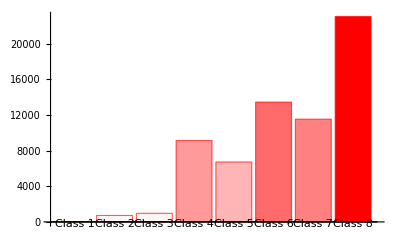

```mathematica
BarChart[sizesClasses[[All,2]],ChartLabels->sizesClasses[[All,1]],ColorFunction->Function[{height}, Opacity[height]],ChartStyle->Red]
```

### Size of classes with different orderings

```mathematica
Table[KeyValueMap[({#1,Length[#2]})&,Values[groupedByClassAllOrderings][[i]]],{i,1,24}]
```

{{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}},{{Class 1,16},{Class 3,960},{Class 2,720},{Class 6,13440},{Class 5,6720},{Class 4,9120},{Class 8,23040},{Class 7,11520}}}

```mathematica
sizesClassesAllOrderings
```

<|{0,1,2,3}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{0,1,3,2}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{0,2,1,3}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{0,2,3,1}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{0,3,1,2}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{0,3,2,1}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{1,0,2,3}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{1,0,3,2}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{1,2,0,3}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{1,2,3,0}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{1,3,0,2}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{1,3,2,0}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{2,0,1,3}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{2,0,3,1}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{2,1,0,3}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{2,1,3,0}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{2,3,0,1}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{2,3,1,0}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{3,0,1,2}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{3,0,2,1}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{3,1,0,2}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{3,1,2,0}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{3,2,0,1}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}},{3,2,1,0}→{{Class 1,16},{Class 2,720},{Class 3,960},{Class 4,9120},{Class 5,6720},{Class 6,13440},{Class 7,11520},{Class 8,23040}}|>

### Amount of non-local AND operations

```mathematica
sizesNLandsSet=KeyValueMap[{#1,#2}&,sizesNLands]
```

{{0,128},{1,6272},{2,37632},{3,21504}}

```mathematica
sizesNLandsSet//MatrixForm
```

(0 | 128
1 | 6272
2 | 37632
3 | 21504)

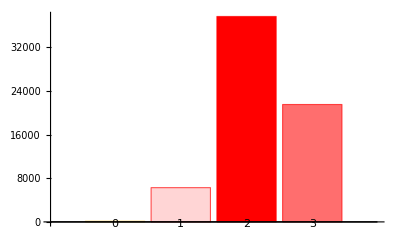

```mathematica
BarChart[sizesNLandsSet[[All,2]],ChartLabels->sizesNLandsSet[[All,1]],ColorFunction->Function[{height}, Opacity[height]],ChartStyle->Red]
```

### Amount of non - local AND operations in the classes

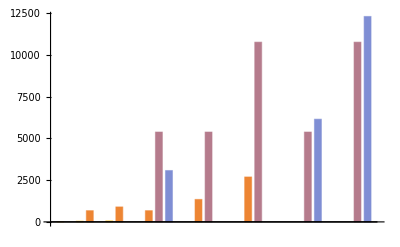

```mathematica
BarChart[sizesNLocalAndsByClass]
```

```mathematica
sizesNLocalAndsByClassAllOrderings
```

```mathematica
<|{0,1,2,3}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{0,1,3,2}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{0,2,1,3}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{0,2,3,1}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{0,3,1,2}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{0,3,2,1}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{1,0,2,3}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{1,0,3,2}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{1,2,0,3}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{1,2,3,0}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{1,3,0,2}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{1,3,2,0}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{2,0,1,3}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{2,0,3,1}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{2,1,0,3}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{2,1,3,0}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{2,3,0,1}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{2,3,1,0}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{3,0,1,2}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{3,0,2,1}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,
{3,1,0,2}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{3,1,2,0}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{3,2,0,1}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>,{3,2,1,0}-><|"Class 1"-><|0->16|>,"Class 2"-><|0->48,1->672|>,"Class 3"-><|0->64,1->896|>,"Class 4"-><|1->672,2->5376,3->3072|>,"Class 5"-><|1->1344,2->5376|>,"Class 6"-><|1->2688,2->10752|>,"Class 7"-><|2->5376,3->6144|>,"Class 8"-><|2->10752,3->12288|>|>|>
```

### Influence of Ordering on Classification

```mathematica
Keys[fNameByClassComb]
```

{{Class 1},{Class 3},{Class 2},{Class 6},{Class 5,Class 6},{Class 4},{Class 8},{Class 7,Class 8},{Class 4,Class 7,Class 8}}

```mathematica
fNameByClassCombSizes=KeyValueMap[({#1,Length[#2]})&,fNameByClassComb]
```

{{{Class 1},16},{{Class 3},960},{{Class 2},720},{{Class 6},4800},{{Class 5,Class 6},15360},{{Class 4},3360},{{Class 8},4224},{{Class 7,Class 8},16128},{{Class 4,Class 7,Class 8},19968}}

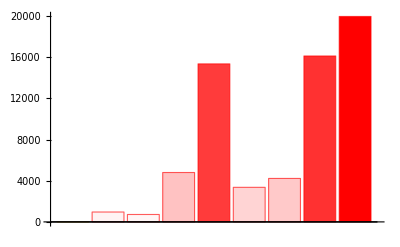

```mathematica
BarChart[fNameByClassCombSizes[[All,2]],ColorFunction->Function[{height}, Opacity[height]],ChartStyle->Red]
```

### Functions

#### Disjointness Function

```mathematica
FNumberFromExpression[1 +a0 b0 + a1 b1 + a0 b0 a1 b1]
```

4959

```mathematica
FunctionTruthTable[4959]//MatrixForm
```

({0,0,0,0}→1
{0,0,0,1}→1
{0,0,1,0}→1
{0,0,1,1}→1
{0,1,0,0}→1
{0,1,0,1}→0
{0,1,1,0}→1
{0,1,1,1}→0
{1,0,0,0}→1
{1,0,0,1}→1
{1,0,1,0}→0
{1,0,1,1}→0
{1,1,0,0}→1
{1,1,0,1}→0
{1,1,1,0}→0
{1,1,1,1}→0)

```mathematica
CanonizedMIS[F[4959]]
```

{II[g,a_0,1,{}],II[g,a_1,2,{a_0}],0,0}

```mathematica
classCombByFunctionName[4959]
```

{Class 4,Class 7,Class 8}

#### Jointness Function

```mathematica
FNumberFromExpression[a0 b0 + a1 b1 + a0 b0 a1 b1]
```

60576

```mathematica
FunctionTruthTable[60576]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→0
{0,0,1,0}→0
{0,0,1,1}→0
{0,1,0,0}→0
{0,1,0,1}→1
{0,1,1,0}→0
{0,1,1,1}→1
{1,0,0,0}→0
{1,0,0,1}→0
{1,0,1,0}→1
{1,0,1,1}→1
{1,1,0,0}→0
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→1)

```mathematica
CanonizedMIS[F[60576]]
```

{II[g,a_0,1,{}],II[g,a_1,2,{a_0}],0,0}

```mathematica
classCombByFunctionName[60576]
```

{Class 4,Class 7,Class 8}

#### Equality Function

```mathematica
FNumberFromExpression[a0 a1+ a0 b1+a0+b0 a1+b0 b1+b0+a1+b1+1]
```

33825

```mathematica
FunctionTruthTable[33825]//MatrixForm
```

({0,0,0,0}→1
{0,0,0,1}→0
{0,0,1,0}→0
{0,0,1,1}→0
{0,1,0,0}→0
{0,1,0,1}→1
{0,1,1,0}→0
{0,1,1,1}→0
{1,0,0,0}→0
{1,0,0,1}→0
{1,0,1,0}→1
{1,0,1,1}→0
{1,1,0,0}→0
{1,1,0,1}→0
{1,1,1,0}→0
{1,1,1,1}→1)

```mathematica
CanonizedMIS[F[33825]]
```

{II[g,a_0 a_1,0,{}],II[g,a_0,1,{a_0 a_1}],II[g,a_1,2,{a_0,a_0 a_1}],0}

```mathematica
classCombByFunctionName[33825]
```

{Class 8}

#### Inequality Function

```mathematica
FNumberFromExpression[a0 a1+ a0 b1+a0+b0 a1+b0 b1+b0+a1+b1]
```

31710

```mathematica
FunctionTruthTable[31710]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→1
{0,0,1,0}→1
{0,0,1,1}→1
{0,1,0,0}→1
{0,1,0,1}→0
{0,1,1,0}→1
{0,1,1,1}→1
{1,0,0,0}→1
{1,0,0,1}→1
{1,0,1,0}→0
{1,0,1,1}→1
{1,1,0,0}→1
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→0)

```mathematica
CanonizedMIS[F[31710]]
```

{II[g,a_0 a_1,0,{}],II[g,a_0,1,{a_0 a_1}],II[g,a_1,2,{a_0,a_0 a_1}],0}

```mathematica
classCombByFunctionName[31710]
```

{Class 8}

#### Exactly - 1 Bit True

```mathematica
SimplifyBinary[a0 (a1+1) (b0 +1)(b1+1)+ (a0+1) a1 (b0+1)( b1+1)+(a0+1)( a1+1) b0 (b1+1)+(a0+1)( a1+1) (b0+1 )b1]
```

a_0+a_1+b_0+a_0 a_1 b_0+b_1+a_0 a_1 b_1+a_0 b_0 b_1+a_1 b_0 b_1

```mathematica
FNumberFromExpression[a0 (a1+1) (b0 +1)(b1+1)+ (a0+1) a1 (b0+1)( b1+1)+(a0+1)( a1+1) b0 (b1+1)+(a0+1)( a1+1) (b0+1 )b1]
```

278

```mathematica
FunctionTruthTable[278]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→1
{0,0,1,0}→1
{0,0,1,1}→0
{0,1,0,0}→1
{0,1,0,1}→0
{0,1,1,0}→0
{0,1,1,1}→0
{1,0,0,0}→1
{1,0,0,1}→0
{1,0,1,0}→0
{1,0,1,1}→0
{1,1,0,0}→0
{1,1,0,1}→0
{1,1,1,0}→0
{1,1,1,1}→0)

```mathematica
CanonizedMIS[F[278]]
```

{II[g,a_0,0,{}],II[g,a_0 a_1,1,{a_0}],0,0}

```mathematica
classCombByFunctionName[278]
```

{Class 5,Class 6}

#### Exactly - 2 Bit True

```mathematica
SimplifyBinary[a0 a1 (b0 +1)(b1+1)+ a0(a1+1) b0(b1+1)+a0 (a1+1) (b0 +1)b1+(a0+1) a1 b0 (b1+1)+(a0+1) a1 (b0 +1)b1+(a0+1) (a1+1) b0 b1]
```

a_0 a_1+a_0 b_0+a_1 b_0+a_0 a_1 b_0+a_0 b_1+a_1 b_1+a_0 a_1 b_1+b_0 b_1+a_0 b_0 b_1+a_1 b_0 b_1

```mathematica
FNumberFromExpression[a0 a1 (b0 +1)(b1+1)+ a0(a1+1) b0(b1+1)+a0 (a1+1) (b0 +1)b1+(a0+1) a1 b0 (b1+1)+(a0+1) a1 (b0 +1)b1+(a0+1) (a1+1) b0 b1]
```

5736

```mathematica
FunctionTruthTable[5736]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→0
{0,0,1,0}→0
{0,0,1,1}→1
{0,1,0,0}→0
{0,1,0,1}→1
{0,1,1,0}→1
{0,1,1,1}→0
{1,0,0,0}→0
{1,0,0,1}→1
{1,0,1,0}→1
{1,0,1,1}→0
{1,1,0,0}→1
{1,1,0,1}→0
{1,1,1,0}→0
{1,1,1,1}→0)

```mathematica
CanonizedMIS[F[5736]]
```

{II[g,a_0 a_1,0,{}],II[g,a_0,1,{a_0 a_1}],0,0}

```mathematica
classCombByFunctionName[5736]
```

{Class 6,Class 5}

#### Exactly - 3 Bit True

```mathematica
FNumberFromExpression[a0 a1 b0 (b1+1)+ a0 a1( b0+1)b1+a0 (a1+1) b0 b1+(a0+1) a1 b0 b1]
```

26752

```mathematica
FunctionTruthTable[26752]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→0
{0,0,1,0}→0
{0,0,1,1}→0
{0,1,0,0}→0
{0,1,0,1}→0
{0,1,1,0}→0
{0,1,1,1}→1
{1,0,0,0}→0
{1,0,0,1}→0
{1,0,1,0}→0
{1,0,1,1}→1
{1,1,0,0}→0
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→0)

```mathematica
CanonizedMIS[F[26752]]
```

{II[g,a_0 a_1,1,{}],II[g,a_0,3,{a_0 a_1}],0,0}

```mathematica
classCombByFunctionName[26752]
```

{Class 6,Class 5}

#### Const - 0

```mathematica
FNumberFromExpression[0]
```

0

```mathematica
CanonizedMIS[F[0]]
```

{0,0,0,0}

```mathematica
classCombByFunctionName[0]
```

{Class 1}

#### Const - 1

```mathematica
FNumberFromExpression[1]
```

65535

```mathematica
CanonizedMIS[F[65535]]
```

{0,0,0,0}

```mathematica
classCombByFunctionName[65535]
```

{Class 1}

#### Parity

```mathematica
FNumberFromExpression[a0+a1+b0+b1]
```

27030

```mathematica
FunctionTruthTable[27030]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→1
{0,0,1,0}→1
{0,0,1,1}→0
{0,1,0,0}→1
{0,1,0,1}→0
{0,1,1,0}→0
{0,1,1,1}→1
{1,0,0,0}→1
{1,0,0,1}→0
{1,0,1,0}→0
{1,0,1,1}→1
{1,1,0,0}→0
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→0)

```mathematica
CanonizedMIS[F[27030]]
```

{II[g,a_0,0,{}],0,0,0}

```mathematica
classCombByFunctionName[27030]
```

{Class 2}

#### Greater Equal Than

```mathematica
FunctionTruthTable[63281]//MatrixForm
```

({0,0,0,0}→1
{0,0,0,1}→0
{0,0,1,0}→0
{0,0,1,1}→0
{0,1,0,0}→1
{0,1,0,1}→1
{0,1,1,0}→0
{0,1,1,1}→0
{1,0,0,0}→1
{1,0,0,1}→1
{1,0,1,0}→1
{1,0,1,1}→0
{1,1,0,0}→1
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→1)

```mathematica
CanonizedMIS[F[63281]]
```

{II[g,a_0 a_1,1,{}],II[g,a_0,2,{a_0 a_1}],II[g,a_1,3,{a_0,a_0 a_1}],0}

```mathematica
classCombByFunctionName[63281]
```

{Class 8,Class 7}

#### Less Than

```mathematica
FunctionTruthTable[2254]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→1
{0,0,1,0}→1
{0,0,1,1}→1
{0,1,0,0}→0
{0,1,0,1}→0
{0,1,1,0}→1
{0,1,1,1}→1
{1,0,0,0}→0
{1,0,0,1}→0
{1,0,1,0}→0
{1,0,1,1}→1
{1,1,0,0}→0
{1,1,0,1}→0
{1,1,1,0}→0
{1,1,1,1}→0)

```mathematica
CanonizedMIS[F[2254]]
```

{II[g,a_0 a_1,1,{}],II[g,a_0,2,{a_0 a_1}],II[g,a_1,3,{a_0,a_0 a_1}],0}

```mathematica
classCombByFunctionName[2254]
```

{Class 8,Class 7}

#### Greater Than

```mathematica
FunctionTruthTable[29456]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→0
{0,0,1,0}→0
{0,0,1,1}→0
{0,1,0,0}→1
{0,1,0,1}→0
{0,1,1,0}→0
{0,1,1,1}→0
{1,0,0,0}→1
{1,0,0,1}→1
{1,0,1,0}→0
{1,0,1,1}→0
{1,1,0,0}→1
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→0)

```mathematica
CanonizedMIS[F[29456]]
```

{II[g,a_0 a_1,0,{}],II[g,a_0,1,{a_0 a_1}],II[g,a_1,2,{a_0,a_0 a_1}],0}

```mathematica
classCombByFunctionName[29456]
```

{Class 8,Class 7}

#### Less Equal Than

```mathematica
FunctionTruthTable[36079]//MatrixForm
```

({0,0,0,0}→1
{0,0,0,1}→1
{0,0,1,0}→1
{0,0,1,1}→1
{0,1,0,0}→0
{0,1,0,1}→1
{0,1,1,0}→1
{0,1,1,1}→1
{1,0,0,0}→0
{1,0,0,1}→0
{1,0,1,0}→1
{1,0,1,1}→1
{1,1,0,0}→0
{1,1,0,1}→0
{1,1,1,0}→0
{1,1,1,1}→1)

```mathematica
CanonizedMIS[F[36079]]
```

{II[g,a_0 a_1,0,{}],II[g,a_0,1,{a_0 a_1}],II[g,a_1,2,{a_0,a_0 a_1}],0}

#### Majority

```mathematica
FNumberFromExpression[a0 a1 b0 (b1+1)+ a0 a1( b0+1)b1+a0 (a1+1) b0 b1+(a0+1) a1 b0 b1+a0 a1 b0 b1]
```

59520

```mathematica
FunctionTruthTable[59520]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→0
{0,0,1,0}→0
{0,0,1,1}→0
{0,1,0,0}→0
{0,1,0,1}→0
{0,1,1,0}→0
{0,1,1,1}→1
{1,0,0,0}→0
{1,0,0,1}→0
{1,0,1,0}→0
{1,0,1,1}→1
{1,1,0,0}→0
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→1)

```mathematica
CanonizedMIS[F[59520]]
```

{II[g,a_0 a_1,1,{}],II[g,a_0,3,{a_0 a_1}],0,0}

```mathematica
classCombByFunctionName[59520]
```

{Class 6}

#### Inner Product Function

```mathematica
FNumberFromExpression[a0 b0+a1 b1]
```

27808

```mathematica
FunctionTruthTable[27808]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→0
{0,0,1,0}→0
{0,0,1,1}→0
{0,1,0,0}→0
{0,1,0,1}→1
{0,1,1,0}→0
{0,1,1,1}→1
{1,0,0,0}→0
{1,0,0,1}→0
{1,0,1,0}→1
{1,0,1,1}→1
{1,1,0,0}→0
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→0)

```mathematica
CanonizedMIS[F[27808]]
```

{II[g,a_0,1,{}],II[g,a_1,2,{a_0}],0,0}

```mathematica
classCombByFunctionName[27808]
```

{Class 4}

#### Index Function

```mathematica
FNumberFromExpression[a0+a0 b0+a1 b0 ]
```

64080

```mathematica
FunctionTruthTable[64080]//MatrixForm
```

({0,0,0,0}→0
{0,0,0,1}→0
{0,0,1,0}→0
{0,0,1,1}→0
{0,1,0,0}→1
{0,1,0,1}→0
{0,1,1,0}→1
{0,1,1,1}→0
{1,0,0,0}→0
{1,0,0,1}→1
{1,0,1,0}→0
{1,0,1,1}→1
{1,1,0,0}→1
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→1)

```mathematica
CanonizedMIS[F[64080]]
```

{II[g,a_0,0,{}],II[g,a_1,1,{a_0}],0,0}

## Test Cases

[“ResultsDataset”]

```mathematica
TestReport[{
TestCreate[Plus[1,1],2]
}]
```

TestReportObject[…]

### RemoveExprFromTerm

```mathematica
TestReport[{
TestCreate[RemoveExprFromTerm[0,0],0],
TestCreate[RemoveExprFromTerm[1,0],1],
TestCreate[RemoveExprFromTerm[1,1],0],
TestCreate[RemoveExprFromTerm[a0,0],a0],
TestCreate[RemoveExprFromTerm[a1,0],a1],
TestCreate[RemoveExprFromTerm[a0,a0],0],
TestCreate[RemoveExprFromTerm[a1,a1],0],
TestCreate[RemoveExprFromTerm[a0,a1],a0],
TestCreate[RemoveExprFromTerm[a1,1],a1],
TestCreate[RemoveExprFromTerm[a0,1],a0],
TestCreate[RemoveExprFromTerm[a0 a1,a0],a0 a1],
TestCreate[RemoveExprFromTerm[a0 a1,a1],a0 a1],
TestCreate[RemoveExprFromTerm[a0 a1,a0 a1],0],
TestCreate[RemoveExprFromTerm[a0 a1+a0,a0],a0 a1],
TestCreate[RemoveExprFromTerm[a0 a1+a0,a1],a0 a1+a0],
TestCreate[RemoveExprFromTerm[a0 a1+a1,a0],a0 a1+a1],
TestCreate[RemoveExprFromTerm[a0 a1+a1,a1],a0 a1],
TestCreate[RemoveExprFromTerm[a0 a1+a0+a1,a1],a0 a1+a0],
TestCreate[RemoveExprFromTerm[a0+a1,a0],a1],
TestCreate[RemoveExprFromTerm[a0+a1,a1],a0],
TestCreate[RemoveExprFromTerm[a0+a1,a0+a1],0],
TestCreate[RemoveExprFromTerm[a0+1,1],a0],
TestCreate[RemoveExprFromTerm[a1+1,a1],1],
TestCreate[RemoveExprFromTerm[a0 a1+1,a0 a1],1],
TestCreate[RemoveExprFromTerm[a0 a1+a0+a1+1,1],a0 a1+a0+a1],
TestCreate[RemoveExprFromTerm[a0 a1+a1,a0 a1],a1],
TestCreate[RemoveExprFromTerm[a0+a1+a0 a1,a0+a0 a1],a1],
TestCreate[RemoveExprFromTerm[a0+a1+a0 a1,a1+a0+a0 a1],0]
}]
```

TestReportObject[…]

### RemoveExprFromTermSet

```mathematica
TestReport[{
TestCreate[RemoveExprFromTermSet[{},0],{}],
TestCreate[RemoveExprFromTermSet[{a0,a1,a0+a1,a0 a1},0],{a0,a1,a0+a1,a0 a1}],
TestCreate[RemoveExprFromTermSet[{a0,a1,a0+a1,a0 a1},a0],{a1,a0 a1}],
TestCreate[RemoveExprFromTermSet[{a0,a1,a0+a1,a0 a1},a1],{a0,a0 a1}],
TestCreate[RemoveExprFromTermSet[{a0+1,a1+1,a0+a1+1,a0 a1+1},1],{a0,a1,a0+a1,a0 a1}],
TestCreate[RemoveExprFromTermSet[{a0+1,a1,a0+a1+1,a0 a1},1],{a0,a1,a0+a1,a0 a1}],
TestCreate[RemoveExprFromTermSet[{a0,a1+1,a0+a1,a0 a1+1},1],{a0,a1,a0+a1,a0 a1}],
TestCreate[RemoveExprFromTermSet[{a0 a1,a0 a1+a1,a0 a1+a0},a0 a1],{a1,a0}],
TestCreate[RemoveExprFromTermSet[{a0+a1,a0},a0],{a1}],
TestCreate[RemoveExprFromTermSet[{a0+a1,a0},a1],{a0}],
TestCreate[RemoveExprFromTermSet[{a0+1,a0 a1+1},1],{a0,a0 a1}],
TestCreate[RemoveExprFromTermSet[{a0+1,a1},1],{a0,a1}],
TestCreate[RemoveExprFromTermSet[{a0,a1,a0+a1,a0 a1},1],{a0,a1,a0+a1,a0 a1}]
}]
```

TestReportObject[…]

### SimplifyBinary

```mathematica
TestReport[{
TestCreate[SimplifyBinary[0],0],
TestCreate[SimplifyBinary[1],1],
TestCreate[SimplifyBinary[2],0],
TestCreate[SimplifyBinary[1+1],0],
TestCreate[SimplifyBinary[1+1+1],1],
TestCreate[SimplifyBinary[3],1],
TestCreate[SimplifyBinary[4],0],
TestCreate[SimplifyBinary[1024],0],
TestCreate[SimplifyBinary[1025],1],
TestCreate[SimplifyBinary[a0],a0],
TestCreate[SimplifyBinary[a0 a0],a0],
TestCreate[SimplifyBinary[a0 a0 a0],a0],
TestCreate[SimplifyBinary[a0 a1],a0 a1],
TestCreate[SimplifyBinary[a0 a0 a1],a0 a1],
TestCreate[SimplifyBinary[a0 a1 a1],a0 a1],
TestCreate[SimplifyBinary[a0 a0 a1 a1],a0 a1],
TestCreate[SimplifyBinary[a0+a0],0],
TestCreate[SimplifyBinary[a0+a0+a0],a0],
TestCreate[SimplifyBinary[a0+a1],a0+a1],
TestCreate[SimplifyBinary[a0+a0+a1],a1],
TestCreate[SimplifyBinary[a0+a0+a1+a1],0],
TestCreate[SimplifyBinary[(a0+a1)a0],a0+a0 a1],
TestCreate[SimplifyBinary[((a0+a1)a0)a1],0],
TestCreate[SimplifyBinary[(a0+a1)a0+a1],a0+a1+a0 a1],
TestCreate[SimplifyBinary[(a0+a1)a0+a0],a0 a1],
TestCreate[SimplifyBinary[(a0+a1)a0+a0 a1],a0],
TestCreate[SimplifyBinary[(a0+1)a1+a1],a0 a1],
TestCreate[SimplifyBinary[(a0+a1+1)a0+a1],a1+a0 a1],
TestCreate[SimplifyBinary[(a0+a1)a0+2],a0+a0 a1],
TestCreate[SimplifyBinary[(a0+a1)a0+3],a0+a0 a1+1]
}]
```

TestReportObject[…]

### ReduceIterateSet

```mathematica
TestReport[{
TestCreate[ReduceIterateSet[{}],{}],
TestCreate[ReduceIterateSet[{a0}],{a0}],
TestCreate[ReduceIterateSet[{a1}],{a1}],
TestCreate[ReduceIterateSet[{a0 a1}],{a0 a1}],
TestCreate[ReduceIterateSet[{a0+a1}],{a0+a1}],
TestCreate[ReduceIterateSet[{a0,a1}],{a0,a1}],
TestCreate[ReduceIterateSet[{a1,a0}],{a1,a0}],
TestCreate[ReduceIterateSet[{a0,a1 a0}],{a0,a0 a1}],
TestCreate[ReduceIterateSet[{a1,a1 a0}],{a1,a0 a1}],
TestCreate[ReduceIterateSet[{a0,a0+a1}],{a0,a1}],
TestCreate[ReduceIterateSet[{a1,a0+a1}],{a1,a0}],
TestCreate[ReduceIterateSet[{a0,a1,a0 a1}],{a0,a1,a0 a1}],
TestCreate[ReduceIterateSet[{a0,a1,a0+a1}],{a0,a1}],
TestCreate[ReduceIterateSet[{a1,a0+a1+a0 a1}],{a1,a0+a0 a1}],
TestCreate[ReduceIterateSet[{a0,a0+a1+a0 a1}],{a0,a1+a0 a1}],
TestCreate[ReduceIterateSet[{a0,a1,a0+a1+a0 a1}],{a0,a1,a0 a1}],
TestCreate[ReduceIterateSet[{a0,a0+a0 a1,a1+a0 a1}],{a0,a0 a1,a1}],
TestCreate[ReduceIterateSet[{a1,a1+a0 a1,a0+a0 a1}],{a1,a0 a1,a0}],
TestCreate[ReduceIterateSet[{a0 a1,a0 a1+a1,a0+a1}],{a0 a1,a1,a0}],
TestCreate[ReduceIterateSet[{a0 a1,a0 a1+a0,a0+a1}],{a0 a1,a0,a1}],
TestCreate[ReduceIterateSet[{a0+a1,a0+a0 a1}],{a0+a1,a0+a0 a1}],
TestCreate[ReduceIterateSet[{a0,a1+a0,a0+a0 a1}],{a0,a1,a0 a1}],
TestCreate[ReduceIterateSet[{a0 a1+a1,a1}],{a0 a1+a1,a1}],
TestCreate[ReduceIterateSet[{a0 a1,a0 a1+a0+a1,a1}],{a0 a1,a0+a1,a1}],
TestCreate[ReduceIterateSet[{a0,a0 a1+a0,a0 a1+a0+a1,a1}],{a0,a0 a1,a1}]
}]
```

TestReportObject[…]

### AddIterateSet

TODO: More Test Cases

```mathematica
TestReport[{
TestCreate[AddIterateSet[{}],{}],
TestCreate[AddIterateSet[{a0}],{a0}],
TestCreate[AddIterateSet[{a1}],{a1}],
TestCreate[AddIterateSet[{a0 a1}],{a0 a1}],
TestCreate[AddIterateSet[{a0+a1}],{a0+a1}],
TestCreate[AddIterateSet[{a0+a1+a0 a1}],{a0+a1+a0 a1}],
TestCreate[AddIterateSet[{a0,a1}],{a0,a1}],
TestCreate[AddIterateSet[{a0,a1,a0+a1}],{a0,a1}],
TestCreate[AddIterateSet[{a0,a1,a0 a1}],{a0,a1,a0 a1}],
TestCreate[AddIterateSet[{a0,a1,a0+a1,a0 a1}],{a0,a1,a0 a1}],
TestCreate[AddIterateSet[{a0,a1+a0 a1,a0+a1+a0 a1}],{a0,a1+a0 a1}],
TestCreate[AddIterateSet[{a0+a1,a0+a0 a1,a1+a0 a1}],{a0+a1,a0+a0 a1}],
TestCreate[AddIterateSet[{a0,a1,a0+a1+a0 a1}],{a0,a1,a0+a1+a0 a1}],
TestCreate[AddIterateSet[{a0+a1,a0+a0 a1,a1+a0 a1}],{a0+a1,a0+a0 a1}],
TestCreate[AddIterateSet[{a0,a1+a0,a0 a1}],{a0,a0 a1,a1+a0}],
TestCreate[AddIterateSet[{a0,a1+a0,a0+a0 a1,a1+a0 a1}],{a0,a1+a0,a0+a0 a1}],
TestCreate[AddIterateSet[{a0,a0 a1,a0+a0 a1}],{a0,a0 a1}],
TestCreate[AddIterateSet[{a0,a1,a0+a0 a1,a0 a1}],{a0,a1,a0 a1}],
TestCreate[AddIterateSet[{a0 a1,a0,a1+a0}],{a0,a0 a1,a1+a0}]
}]
```

TestReportObject[…]

### ConditionalSet

```mathematica
TestReport[DeleteDuplicates[{
TestCreate[ConditionalSet[{}],{}],
TestCreate[ConditionalSet[{a0}],{a0}],
TestCreate[ConditionalSet[{a1}],{a1}],
TestCreate[ConditionalSet[{a0+a1}],{a0+a1}],
TestCreate[ConditionalSet[{a0 a1+a0}],{a0 a1+a0}],
TestCreate[ConditionalSet[{a0 a1+a1}],{a0 a1+a1}],
TestCreate[ConditionalSet[{1}],{}],
TestCreate[ConditionalSet[{a0+1}],{a0}],
TestCreate[ConditionalSet[{a1+1}],{a1}],
TestCreate[ConditionalSet[{a0+a1+1}],{a0+a1}],
TestCreate[ConditionalSet[{a0 a1+a0+1}],{a0 a1+a0}],
TestCreate[ConditionalSet[{a0 a1+a1+1}],{a0 a1+a1}],
TestCreate[ConditionalSet[{a0,a1}],{a0,a1}],
TestCreate[ConditionalSet[{a0,a0 a1}],{a0,a0 a1}],
TestCreate[ConditionalSet[{a1,a0 a1}],{a1,a0 a1}],
TestCreate[ConditionalSet[{a0,a1,a0 a1}],{a0,a1}],
TestCreate[ConditionalSet[{a0+1,a1+1}],{a0,a1}],
TestCreate[ConditionalSet[{a0+1,a0 a1+1}],{a0,a0 a1}],
TestCreate[ConditionalSet[{a1+1,a0 a1+1}],{a1,a0 a1}],
TestCreate[ConditionalSet[{a0+1,a1+1,a0 a1+1}],{a0,a1}],
TestCreate[ConditionalSet[{a0,a0+a1}],{a0,a1}],
TestCreate[ConditionalSet[{a0,a0 a1+a0}],{a0,a0 a1}],
TestCreate[ConditionalSet[{a0,a0+a1}],{a0,a1}],
TestCreate[ConditionalSet[{a1,a0 a1+a1}],{a1,a0 a1}],
TestCreate[ConditionalSet[{a0 a1,a0 a1+a0}],{a0,a0 a1}],
TestCreate[ConditionalSet[{a0 a1,a0 a1+a1}],{a1,a0 a1}],
TestCreate[ConditionalSet[{a0,a0+a0 a1,a0 a1}],{a0,a0 a1}],
TestCreate[ConditionalSet[{a0,a0+a0 a1,a0 a1}],{a0,a0 a1}],
TestCreate[ConditionalSet[{a0+1,a0 a1+1,a0+a0 a1+1}],{a0,a0 a1}],
TestCreate[ConditionalSet[{a1,a0 a1+a1+a0}],{a1,a0+a0 a1}],
TestCreate[ConditionalSet[{a1+a0,a0 a1+a1+a0}],{a0 a1,a0+a1}],
TestCreate[ConditionalSet[{a1+a0,a0 a1+a1+a0,a0 a1+a0}],{a0,a1}],
TestCreate[ConditionalSet[{a0 a1+a0,a0 a1+a1+a0,a1}],{a1,a0+a0 a1}],
TestCreate[ConditionalSet[{a0 a1+a0,a0 a1+a1+a0,a0}],{a0,a1}],
TestCreate[ConditionalSet[{a0,a0 a1+ a0,a0 a1+a1}],{a0,a1}],
TestCreate[ConditionalSet[{a1+a0 a1, a0 a1+a0, a0 a1+a1+a0}],{a0,a1}],
TestCreate[ConditionalSet[{a0+a1,a0+a1+a0 a1,a1+a0 a1,a0+a0 a1}],{a0,a1}],
TestCreate[ConditionalSet[{a0+a1+a0 a1,a0 a1,a0}],{a0,a1}],
TestCreate[ConditionalSet[{a0+a1,a0 a1+a1,a0 a1+a0}],{a0+a1,a0+a0 a1}],
TestCreate[ConditionalSet[{a0+a1+a0 a1,a0+a1,a0 a1}],{a0 a1,a0+a1}],
TestCreate[ConditionalSet[{a0,a1+a0 a1,a0 a1+a0}],{a0,a1}],
TestCreate[ConditionalSet[{a0 a1,a0+a0 a1,a1+a0 a1,a0+a1+a0 a1}],{a0, a1}],
TestCreate[ConditionalSet[{a0+a1}],{a0+a1}],
TestCreate[ConditionalSet[{a0+a1,a0}],{a0,a1}],
TestCreate[ConditionalSet[{a0+1,a1+1}],{a0,a1}],
TestCreate[ConditionalSet[{a0+a1+1}],{a0+a1}],
TestCreate[ConditionalSet[{a0,a0+a1+1}],{a0,a1}],
TestCreate[ConditionalSet[{a1,a0+a1+1}],{a0,a1}],
TestCreate[ConditionalSet[{a0+1,a0+a1}],{a0,a1}],
TestCreate[ConditionalSet[{a1+1,a0+a1}],{a0,a1}],
TestCreate[ConditionalSet[{a0 a1}],{a0 a1}],
TestCreate[ConditionalSet[{a0 a1+1}],{a0 a1}],
TestCreate[ConditionalSet[{a0,a1,a0+a1+1}],{a0,a1}],
TestCreate[ConditionalSet[{a0,a1,a0 a1+a1+1}],{a0,a1}]
}]]
```

TestReportObject[…]

### Reduction

Todo : more testcases

```mathematica
TestReport[{
TestCreate[Reduction[a1,{a1}],{0,{a1}}],
TestCreate[Reduction[a0,{a0}],{0,{a0}}],
TestCreate[Reduction[a0 a1,{a0 a1}],{0,{a0 a1}}],
TestCreate[Reduction[a0+a0 a1,{a0+a0 a1}],{0,{a0+a0 a1}}],
TestCreate[Reduction[a1+a0 a1,{a1+a0 a1}],{0,{a1+a0 a1}}],
TestCreate[Reduction[a0+a1+a0 a1,{a0+a1+a0 a1}],{0,{a0+a1+a0 a1}}],
TestCreate[Reduction[a0,{a1}],{a0,{a1}}],
TestCreate[Reduction[a1,{a0}],{a1,{a0}}],
TestCreate[Reduction[a0 a1,{a1}],{a0 a1,{a1}}],
TestCreate[Reduction[a0 a1,{a0}],{a0 a1,{a0}}],
TestCreate[Reduction[a0+a1,{a0 a1}],{a0+a1,{a0 a1}}],
TestCreate[Reduction[a0+a1,{a0}],{a1,{a0}}],
TestCreate[Reduction[a0+a1,{a1}],{a0,{a1}}],
TestCreate[Reduction[a0,{a0+a1,a1}],{0,{a0,a1}}],
TestCreate[Reduction[a1,{a0+a1,a0}],{0,{a0,a1}}],
TestCreate[Reduction[a0 a1,{a0,a1}],{0,{a0,a1}}],
TestCreate[Reduction[a0 + a1,{a0 a1, a0}],{a1,{a0,a0 a1}}],
TestCreate[Reduction[a0+a1,{a0, a1}],{0,{a0,a1}}],
TestCreate[Reduction[a0+a1,{a0+a1}],{0,{a0+a1}}],
TestCreate[Reduction[a1+a0 a1,{a1+a0, a0+a0 a1}],{0,{a0+a1,a0+a0 a1}}],
TestCreate[Reduction[a0+a0 a1,{a1+a0, a1+a0 a1}],1{0,{a0+a1,a1+a0 a1}}],
TestCreate[Reduction[a0+a0 a1,{a1+a0, a0 a1}],{a0,{a0 a1,a0+a1}}],
TestCreate[Reduction[a1+a0 a1,{a1+a0, a0 a1}],{a1,{a0 a1,a0+a1}}],
TestCreate[Reduction[a1+a0 a1, {a1+a0, a0+a0 a1, a1+a0 a1}],{0,{a0+a1,a0+a0 a1}}],
TestCreate[Reduction[a0,{a0,a1}],{0,{a0,a1}}],
TestCreate[Reduction[a1,{a0,a1}],{0,{a0,a1}}],
TestCreate[Reduction[a0 a1,{a0,a1}],{0,{a0,a1}}],
TestCreate[Reduction[a0+a1,{a0,a1}],{0,{a0,a1}}],
TestCreate[Reduction[a0+a0 a1,{a0,a1}],{0,{a0,a1}}],
TestCreate[Reduction[a1+a0 a1,{a0,a1}],{0,{a0,a1}}],
TestCreate[Reduction[a1+a0 a1,{a0,a1}],{0,{a0,a1}}],
TestCreate[Reduction[a0+a1+a0 a1,{a0,a1}],{0,{a0,a1}}]
}]
```

TestReportObject[…]

### Non-local Ands

#### 0 Non - local Ands

Generate expressions with zero non-local ands. 2^7=128 should be all possible expressions with 0 non-local ands.

```mathematica
CreateExprWith0NLAnds=Module[{AllSubsets,SummedSubsets},
(* Generate all subsets of the terms with no non-local and. *)
AllSubsets=Subsets[{1,a0,a1,a0 a1,b0,b1,b0 b1}];

(* Sum up the subsets *)
SummedSubsets=Total/@AllSubsets;

(* Delete duplicate values and return *)
DeleteDuplicates[SummedSubsets]
];
```

Test for all generated expressions if the function call returns 0.

```mathematica
TestReport[(TestCreate[CountNLAndInExpr[#],0])&/@CreateExprWith0NLAnds]
```

TestReportObject[…]

#### 1 Non - local And

Generate expressions with exactly 1 non - local and .

```mathematica
CreateExprWith1NLAnd=Module[{Aside,Bside,OneNonLocalAnd},
(* Multiply the expressions only containing a or b values *)
Aside=Total/@Subsets[{a0,a1,a0 a1},{1,3}];
Bside=Total/@Subsets[{b0,b1,b0 b1},{1,3}];
OneNonLocalAnd=Flatten[TensorProduct[Aside,Bside]];

(* Add expressions with 0 non-local ands to the expressions with one non-local and *)
OneNonLocalAnd=(OneNonLocalAnd+#)&/@CreateExprWith0NLAnds;

Flatten[OneNonLocalAnd]
];
```

Test for all generated expressions if the function call return 1.

```mathematica
TestReport[(TestCreate[CountNLAndInExpr[#],1])&/@CreateExprWith1NLAnd]
```

TestReportObject[<|Title -> Automatic, «6», TestsSucceededKeys -> {9149739545781757750, 4660875562483037724, 1943698554330444248, 6775646286899305168, 3708580646122561586, 5921012695352247557, 7030597766128862634, 3724958021283310478, 7034944140916399415, <<18>>7, «6257», 1920714437171819930, 7962563958123313880, 8541787185575894579, 8957834665418884926, 513875296881543621}|>]

#### 2 Non - local Ands

```mathematica
CreateExprWith2NLAnd=Module[{Aside,Bside,Mul1,Mul2,TwoNonLocalAnd},
(* Multiply the expressions only containing a or b values *)
Aside=Subsets[Total/@Subsets[{a0,a1,a0 a1},{1,3}],{2}];
Bside=Subsets[Total/@Subsets[{b0,b1,b0 b1},{1,3}],{2}];

Mul1=Flatten[(Function[bs,#*bs]/@Bside)&/@Aside,1];
Mul2=Flatten[(Function[bs,#*Reverse[bs]]/@Bside)&/@Aside,1];

TwoNonLocalAnd=Total/@Union[Mul1,Mul2];
TwoNonLocalAnd=(TwoNonLocalAnd+#)&/@CreateExprWith0NLAnds;

DeleteDuplicates[SimplifyBinary[ExpandAll[Flatten[TwoNonLocalAnd]]]]
];
```

```mathematica
TestReport[(TestCreate[CountNLAndInExpr[#],2])&/@CreateExprWith2NLAnd]
```

TestReportObject[<|Title -> Automatic, «6», TestsSucceededKeys -> {2528108150115568371, 7997878879634181567, 4883183376673047708, 3804019680600926256, 8012543848225180661, 8768411098868660543, 5757222255153577300, 8709971156954979658, 3139559521870435134, <<18>>5, «37617», 8008319330165123036, 600562793174167689, 413660463936586989, 2157398289913758044, 2144991288027011846}|>]

#### 3 Non - local Ands

```mathematica
CreateExprWith3NLAnd2=Module[{Aside,Bside,TwoNonLocalAnd1,TwoNonLocalAnd2,TwoNonLocalAnd3,TwoNonLocalAnd4,TwoNonLocalAnd5,TwoNonLocalAnd6,TwoNonLocalAnd},
(* Multiply the expressions only containing a or b values *)
Aside=Subsets[Total/@Subsets[{a0,a1,a0 a1},{1,3}],{3}];
Bside=Subsets[Total/@Subsets[{b0,b1,b0 b1},{1,3}],{3}];

Aside=DeleteCases[Aside,x_/;Length[ReduceIterateSet[x]]<3];
Bside=DeleteCases[Bside,x_/;Length[ReduceIterateSet[x]]<3];

Aside=(SplitAddition/@#)&/@Aside;
Bside=(SplitAddition/@#)&/@Bside;

TwoNonLocalAnd1=Flatten[(Function[as,{Flatten[TensorProduct[as[[1]],#[[1]]]],Flatten[TensorProduct[as[[2]],#[[2]]]],Flatten[TensorProduct[as[[3]],#[[3]]]]}]/@Aside)&/@Bside,1];
TwoNonLocalAnd2=Flatten[(Function[as,{Flatten[TensorProduct[as[[1]],#[[1]]]],Flatten[TensorProduct[as[[2]],#[[3]]]],Flatten[TensorProduct[as[[3]],#[[2]]]]}]/@Aside)&/@Bside,1];
TwoNonLocalAnd3=Flatten[(Function[as,{Flatten[TensorProduct[as[[1]],#[[2]]]],Flatten[TensorProduct[as[[2]],#[[1]]]],Flatten[TensorProduct[as[[3]],#[[3]]]]}]/@Aside)&/@Bside,1];
TwoNonLocalAnd4=Flatten[(Function[as,{Flatten[TensorProduct[as[[1]],#[[2]]]],Flatten[TensorProduct[as[[2]],#[[3]]]],Flatten[TensorProduct[as[[3]],#[[1]]]]}]/@Aside)&/@Bside,1];
TwoNonLocalAnd5=Flatten[(Function[as,{Flatten[TensorProduct[as[[1]],#[[3]]]],Flatten[TensorProduct[as[[2]],#[[1]]]],Flatten[TensorProduct[as[[3]],#[[2]]]]}]/@Aside)&/@Bside,1];
TwoNonLocalAnd6=Flatten[(Function[as,{Flatten[TensorProduct[as[[1]],#[[3]]]],Flatten[TensorProduct[as[[2]],#[[2]]]],Flatten[TensorProduct[as[[3]],#[[1]]]]}]/@Aside)&/@Bside,1];
TwoNonLocalAnd=Union[TwoNonLocalAnd1,TwoNonLocalAnd2,TwoNonLocalAnd3,TwoNonLocalAnd4,TwoNonLocalAnd5,TwoNonLocalAnd6];

TwoNonLocalAnd=(Total[#,2])&/@DeleteCases[TwoNonLocalAnd,x_/;Or[ContainsAll[x[[1]],x[[2]]],ContainsAll[x[[2]],x[[1]]], ContainsAll[x[[1]],x[[3]]],ContainsAll[x[[2]],x[[3]]]]];
TwoNonLocalAnd=DeleteDuplicates[SimplifyBinary[TwoNonLocalAnd]];
TwoNonLocalAnd=(TwoNonLocalAnd+#)&/@CreateExprWith0NLAnds;

DeleteElements[DeleteDuplicates[SimplifyBinary[ExpandAll[Flatten[TwoNonLocalAnd]]]],CreateExprWith2NLAnd]
];
```

```mathematica
TestReport[(TestCreate[CountNLAndInExpr2[#],3])&/@CreateExprWith3NLAnd2]
```

TestReportObject[<|Title -> Automatic, «6», TestsSucceededKeys -> {7848634776509020876, 8324492086428344814, 6169371337737109444, 1819128317399269358, 7384758236154662827, 7739901135816567832, 8939030421615194298, 7355271691574587954, 7107795313368878404, <<19>>, «21489», 4340364348021328599, 4699244305342196038, 4776921820958200285, 2587869091802945634, 4473669126360129649}|>]

#### Manual Tests

```mathematica
TestReport[{
TestCreate[CountNLAndInExpr[a0 b0+a1 b1],2],
TestCreate[CountNLAndInExpr[a0 b1+a1 b0],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+a0],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+a1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+a0 a1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+a0+a0 a1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+a1+a0 a1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+a0+a1+a0 a1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b0],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b0 b1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b0+b0 b1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b1+b0 b1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b0+b1+b0 b1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b0+a0],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b1+a0],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b0 b1+a0 a1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+b0+a0 a1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+a1+b0 b1],2],
TestCreate[CountNLAndInExpr[a0 b0+a1 b1+a0+b1+a0 a1],2],
TestCreate[CountNLAndInExpr[a1(b0 +1)+a0 a1(b1)],2],
TestCreate[CountNLAndInExpr[a0 a1(b0 +1)+a0(b1)],2],
TestCreate[CountNLAndInExpr[a0 a1(b0 +b1)+a0(b1)],2],
TestCreate[CountNLAndInExpr[a0 (b0 +b1+1)+a0 a1(b1 b0)],2],
TestCreate[CountNLAndInExpr[a0 a1(b0 +b1)+a0(b1)],2]
}]
```

TestReportObject[…]